```mathematica
Needs["ErrorBarPlots`"]
```

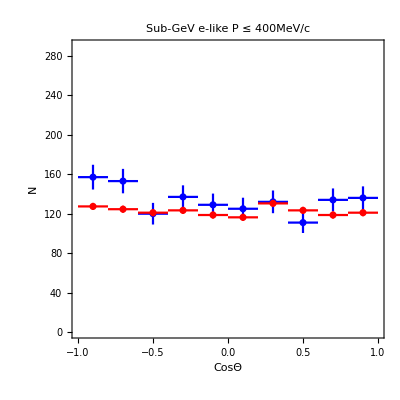

```mathematica
costheta=Table[-1.1+0.2*i,{i,1,10}];
expsubGeVelikeless={157,153,120,137,129,125,132,111,134,136};
expsubGeVelikelesserror={12.53,12.37,10.95,11.70,11.36,11.18,11.49,10.53,11.57,11.66};
expmcsubGeVelikeless={127.37,124.55,121.025,123.375,118.675,116.325,130.425,123.375,118.675,121.025};

plotexpsubGeVelikeless=ErrorListPlot[Table[{{costheta[[i]],expsubGeVelikeless[[i]]},ErrorBar[0.1,expsubGeVelikelesserror[[i]]]},
{i,1,10}],Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Blue];

plotmcsubGeVelikeless=ErrorListPlot[Table[{{costheta[[i]],expmcsubGeVelikeless[[i]]},ErrorBar[0.1,3.57]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},PlotStyle->Red, FrameLabel->{"CosΘ","N"}];

Show[{plotexpsubGeVelikeless,plotmcsubGeVelikeless},PlotLabel-> "Sub-GeV e-like P ≤ 400MeV/c"]
```

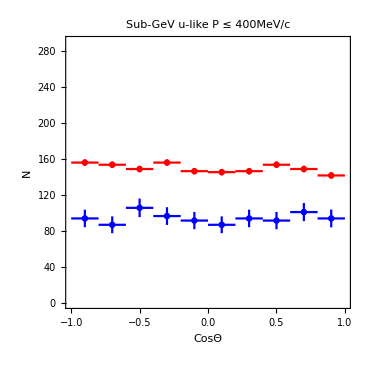

```mathematica
expsubGeVulikeless={94,86.95,105.75,96.65,91.65,86.95,94,91.65,101.05,94};
expsubGeVulikelesserror={9.69,9.32,10.28,9.83,9.57,9.32,9.69,9.57,10.05,9.9};
expmcsubGeVulikeless={155.95,153.57,148.81,155.95,146.43,145.34,146.43,153.57,148.81,141.67};
expmcsubGeVulikelesserror=3.57;
expsubGeVulikeratioless=Table[{expsubGeVulikeless[[i]]/expmcsubGeVulikeless[[i]],((expsubGeVulikelesserror[[i]]/expmcsubGeVulikeless[[i]])^2+ 
(expsubGeVulikeless[[i]]expmcsubGeVulikelesserror/expmcsubGeVulikeless[[i]]^2)^2)^0.5},{i,1,10}];




plotexpsubGeVulikeratioless=ErrorListPlot[Table[{{costheta[[i]],expsubGeVulikeratioless[[i,1]]},ErrorBar[0.1,expsubGeVulikeratioless[[i,2]]]},{i,1,10}],Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,1}}];





plotexpsubGeVulikeless=ErrorListPlot[Table[{{costheta[[i]],expsubGeVulikeless[[i]]},ErrorBar[0.1,expsubGeVulikelesserror[[i]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Blue];

plotmcsubGeVulikeless=ErrorListPlot[Table[{{costheta[[i]],expmcsubGeVulikeless[[i]]},ErrorBar[0.1,3.57]},{i,1,10}],Axes->None,Frame->True,
AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Red];

Show[{plotexpsubGeVulikeless,plotmcsubGeVulikeless},PlotLabel-> "Sub-GeV u-like P ≤ 400MeV/c"]
```

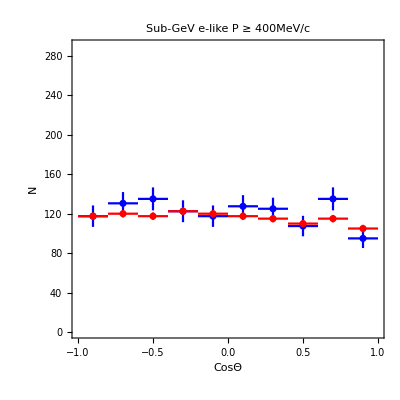

```mathematica
costheta=Table[-1.1+0.2*i,{i,1,10}];
expsubGeVelike={117.5,130.5,135,122.5,117.5,127.5,125,107.5,135,95};
expsubGeVelikeError={10.84,11.4,11.62,11.07,10.84,11.29,11.18,10.37,11.62,9.747};
expmcsubGeVelike={117.5,120,117.5,122.5,120,117.5,115,110,115,105};

plotexpsubGeVelike=ErrorListPlot[Table[{{costheta[[i]],expsubGeVelike[[i]]},ErrorBar[0.1,expsubGeVelikeError[[i]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Blue];

plotmcsubGeVelike=ErrorListPlot[Table[{{costheta[[i]],expmcsubGeVelike[[i]]},ErrorBar[0.1,3.75]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Red];

Show[{plotexpsubGeVelike,plotmcsubGeVelike},PlotLabel-> "Sub-GeV e-like P ≥ 400MeV/c"]
```

{{0.680614,0.058198},{0.428916,0.0454773},{0.526138,0.0508559},{0.64618,0.0569249},{0.706619,0.0610315},{0.719163,0.0602328},{0.934888,0.070923},{0.89141,0.0636017},{0.934888,0.070923},{1.03272,0.0748474}}

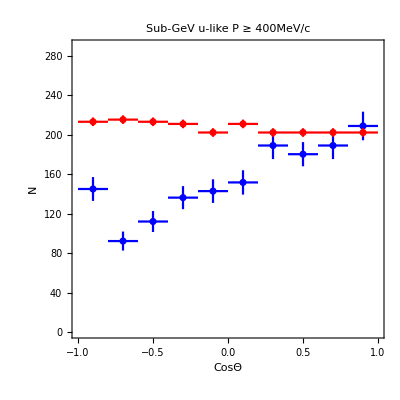

```mathematica
costheta=Table[-1.1+0.2*i,{i,1,10}];
expsubGeVμlike={145,92.31,112.09,136.26,142.86,151.65,189.01,180.22,189.01,208.79};
expsubGeVμlikeError={12.04,9.608,10.59,11.67,11.95,12.31,13.75,12.26,13.75,14.45};
expmcsubGeVμlike={213.043,215.217,213.043,210.870,202.174,210.870,202.174,202.174,202.174,202.174};
expmcsubGeVμlikeerror=Table[4.35,{i,1,10}];

expsubGeVμlikeratio=Table[{expsubGeVμlike[[i]]/expmcsubGeVμlike[[i]],((expsubGeVμlikeError[[i]]/expmcsubGeVμlike[[i]])^2+ (expsubGeVμlike[[i]]expmcsubGeVμlikeerror[[i]]/expmcsubGeVμlike[[i]]^2)^2)^0.5},{i,1,10}]
plotexpsubGeVμlikeratio= ErrorListPlot[Table[{{costheta[[i]],expsubGeVμlikeratio[[i,1]]},ErrorBar[0.1,expsubGeVμlikeratio[[i,2]]]}, {i,1,10}]];


plotexpsubGeVμlike=ErrorListPlot[Table[{{costheta[[i]],expsubGeVμlike[[i]]},ErrorBar[0.1,expsubGeVμlikeError[[i]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,FrameLabel->{"CosΘ","N"},PlotStyle->Blue,PlotRange->{{-1,1},{0,290}}];

plotmcsubGeVμlike=ErrorListPlot[Table[{{costheta[[i]],expmcsubGeVμlike[[i]]},ErrorBar[0.1,4.35]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Red];

Show[{plotexpsubGeVμlike,plotmcsubGeVμlike},PlotLabel-> "Sub-GeV u-like P ≥ 400MeV/c"]
```

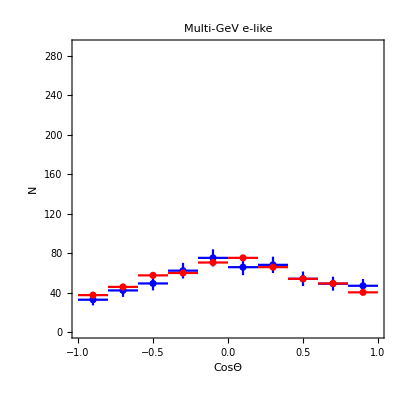

```mathematica
expMultiGeVelike={32.94,42.35,49.41,62.35,75.29,65.88,68.24,54.12,49.17,47.06};
expMultiGeVelikeerror={5.74,6.51,7.03,7.90,8.68,8.12,8.26,7.36,7.05,6.86};
expMCMultiGeVelike={37.6,45.9,57.6,60.0,70.6,75.3,65.9,54.1,49.4,40.4};


plotexpMultiGeVelike=ErrorListPlot[Table[{{costheta[[i]],expMultiGeVelike[[i]]},ErrorBar[0.1,expMultiGeVelikeerror[[i]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Blue];

plotexpMCMultiGeVelike=ErrorListPlot[Table[{{costheta[[i]],expMCMultiGeVelike[[i]]},ErrorBar[0.1,2.35]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},FrameLabel->{"CosΘ","N"},PlotStyle->Red];

Show[{plotexpMultiGeVelike,plotexpMCMultiGeVelike},PlotLabel-> "Multi-GeV e-like"]
```

{{0.466809,0.0577535},{0.505085,0.0599473},{0.439275,0.0530312},{0.523476,0.0537951},{0.605362,0.054875},{0.865359,0.0701558},{0.860007,0.0721004},{0.947897,0.0799583},{0.971234,0.0886141},{0.963192,0.0846847}}

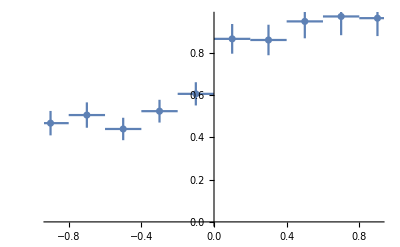

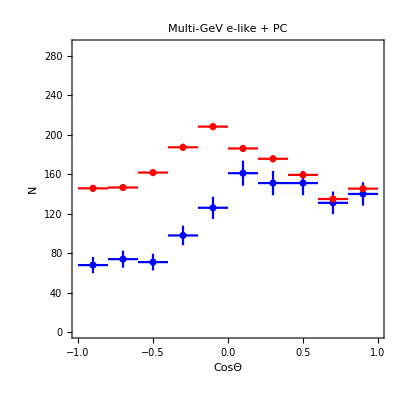

```mathematica
expMultiGeVμlike={68,74,71,98,126,161,151,151,131,140};
expMultiGeVμlikeerror={8.25,8.60,8.43,9.90,11.22,12.69,12.29,12.29,11.45,11.83};
expMCMultiGeVμlike={145.67,146.51,161.63,187.21,208.14,186.05,175.58,159.30,134.88,145.35};
expMCMultiGeVμlikeerror=3.53;

expMCMultiGeVμlikeratio=Table[{expMultiGeVμlike[[i]]/expMCMultiGeVμlike[[i]],((expMultiGeVμlikeerror[[i]]/expMCMultiGeVμlike[[i]])^2+ (expMultiGeVμlike[[i]]expMCMultiGeVμlikeerror/expMCMultiGeVμlike[[i]]^2)^2)^0.5},{i,1,10}]
plotexpMCMultiGeVμlikeratio=ErrorListPlot[Table[{{costheta[[i]],expMCMultiGeVμlikeratio[[i,1]]},ErrorBar[0.1,expMCMultiGeVμlikeratio[[i,2]]]},{i,1,10}]]

plotexpMultiGeVμlike=ErrorListPlot[Table[{{costheta[[i]],expMultiGeVμlike[[i]]},ErrorBar[0.1,expMultiGeVμlikeerror[[i]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},PlotStyle->Blue,FrameLabel->{"CosΘ","N"}];
plotexpMCMultiGeVμlike=ErrorListPlot[Table[{{costheta[[i]],expMCMultiGeVμlike[[i]]},ErrorBar[0.1,3.53]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotRange->{{-1,1},{0,290}},PlotStyle->Red,FrameLabel->{"CosΘ","N"}];

Show[{plotexpMultiGeVμlike,plotexpMCMultiGeVμlike},PlotLabel-> "Multi-GeV e-like + PC"]
```

```mathematica
costheta=Table[-1.1+0.2*i,{i,1,10}]
Pct=costheta[[6;;10]];(*NOT NEEDED?*)
R=6371 (*in Km*)
L=Table[If[i>5,(6.4/costheta[[i]])Log[1030/(120costheta[[i]])],
-2*R*costheta[[i]]+(6.4/Abs[costheta[[i]]])Log[1030/(120Abs[costheta[[i]]])]],{i,1,10}]
```

{-0.9,-0.7,-0.5,-0.3,-0.1,0.1,0.3,0.5,0.7,0.9}

6371

{11483.8,8942.32,6407.39,3894.15,1559.15,284.954,71.5476,36.39,22.9165,16.0369}

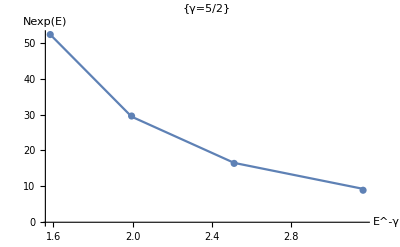

```mathematica
Nmuon1={52.3,29.6,16.4,8.92};
Energy1={1.585,1.995,2.512,3.162};
gamma1={1.585^(-5/2),1.995^(-5/2),2.512^(-5/2),3.162^(-5/2)};
plotNmuon1=ListPlot[Table[{Energy1[[i]],Nmuon1[[i]]},{i,1,4}]];
confact1=52.3/(1.585^(-5/2));
plotgamma1=ListLinePlot[Table[{Energy1[[i]],gamma1[[i]]*confact1},{i,1,4}]];
Show[{plotNmuon1},{plotgamma1},AxesLabel->{"E^-γ","Nexp(E)"} ,PlotLabel->{"γ=5/2"}]
```

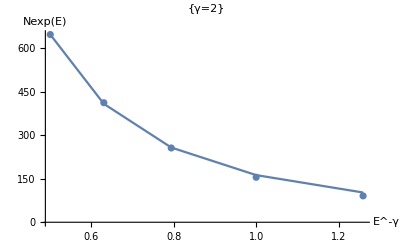

```mathematica
Nmuon2={647,412,256,155,90.9};
Energy2={0.5012,0.631,0.7943,1,1.259};
gamma2={0.5012^(-2),0.631^(-2),0.7943^(-2),1^(-2),1.259^(-2)};
confact2=647/(0.5012^(-2));
PlotNmuon2=ListPlot[Table[{Energy2[[i]],Nmuon2[[i]]},{i,1,5}]];
Plotgamma2=ListLinePlot[Table[{Energy2[[i]],gamma2[[i]]*confact2},{i,1,5}]];
Show[{PlotNmuon2},{Plotgamma2},AxesLabel->{"E^-γ","Nexp(E)"} ,PlotLabel->{"γ=2"}]
```

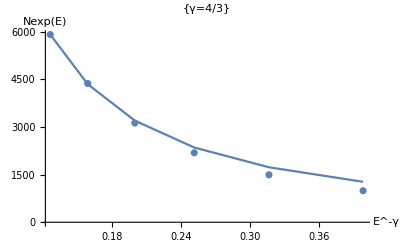

```mathematica
Nmuon3={5913,4372,3124,2188,1494,994};
Energy3={0.1259,0.1585,0.1995,0.2512,0.3162,0.3981};
gamma3={0.1259^(-4/3),0.1585^(-4/3),0.1995^(-4/3),0.2512^(-4/3),0.3162^(-4/3),0.3981^(-4/3)};
confact3=5913/(0.1259^(-4/3));
plotNmuon3=ListPlot[Table[{Energy3[[i]],Nmuon3[[i]]},{i,1,6}]];
plotgamma3=ListLinePlot[Table[{Energy3[[i]],gamma3[[i]]*confact3},{i,1,6}]];
Show[{plotNmuon3},{plotgamma3},AxesLabel->{"E^-γ","Nexp(E)"} ,PlotLabel->{"γ=4/3"}]
```

```mathematica
γ={5/2,2,4/3};
e1={1.33,0.4,0.1};
e2={5,1.33,0.4};
convertNU=1/(1.973*10^-7)*1000/10^9;
expectednumberwithoutoscillations1=Integrate[e^(-γ[[1]]),{e,e1[[1]],e2[[1]]}];
p=1-Sin[(L)m2/(4e)*convertNU]^2 ;

expectednumberWITHoscillations1=Integrate [e^(-γ[[1]]) p,{e,e1[[1]],e2[[1]]}];
Rexp1=expectednumberWITHoscillations1/expectednumberwithoutoscillations1

expectednumberwithoutoscillations2=Integrate[e^(-γ[[2]]),{e,e1[[2]],e2[[2]]}];
expectednumberWITHoscillations2=Integrate [e^(-γ[[2]]) p,{e,e1[[2]],e2[[2]]}];
Rexp2=expectednumberWITHoscillations2/expectednumberwithoutoscillations2

expectednumberwithoutoscillations3=Integrate[e^(-γ[[3]]),{e,e1[[3]],e2[[3]]}];
expectednumberWITHoscillations3=Integrate [e^(-γ[[3]]) p,{e,e1[[3]],e2[[3]]}];
Rexp3=expectednumberWITHoscillations3/expectednumberwithoutoscillations3
```

{(2.66657 (1.26222×10^-7 FresnelS[60.8723 √m2]-1.26222×10^-7 FresnelS[118.026 √m2]+√m2 (0.187507 m2-7.68343×10^-6 Sin[5820.5 m2]+0.0000148975 Sin[21881.6 m2])))/m2^(3/2),(2.66657 (1.83692×10^-7 FresnelS[53.7157 √m2]-1.83692×10^-7 FresnelS[104.15 √m2]+√m2 (0.187507 m2-9.86716×10^-6 Sin[4532.34 m2]+0.0000191316 Sin[17038.9 m2])))/m2^(3/2),(2.66657 (3.02861×10^-7 FresnelS[45.4692 √m2]-3.02861×10^-7 FresnelS[88.161 √m2]+√m2 (0.187507 m2-0.0000137709 Sin[3247.54 m2]+0.0000267005 Sin[12208.8 m2])))/m2^(3/2),(2.66657 (6.39215×10^-7 FresnelS[35.4473 √m2]-6.39215×10^-7 FresnelS[68.7293 √m2]+√m2 (0.187507 m2-0.0000226584 Sin[1973.72 m2]+0.0000439328 Sin[7420. m2])))/m2^(3/2),(2.66657 (2.52309×10^-6 FresnelS[22.4296 √m2]-2.52309×10^-6 FresnelS[43.4891 √m2]+√m2 (0.187507 m2-0.0000565917 Sin[790.245 m2]+0.000109727 Sin[2970.85 m2])))/m2^(3/2),(2.66657 (0.0000322926 FresnelS[9.58879 √m2]-0.0000322926 FresnelS[18.5919 √m2]+√m2 (0.187507 m2-0.000309647 Sin[144.427 m2]+0.00060038 Sin[542.958 m2])))/m2^(3/2),(2.66657 (0.000256669 FresnelS[4.80479 √m2]-0.000256669 FresnelS[9.31608 √m2]+√m2 (0.187507 m2-0.00123324 Sin[36.2634 m2]+0.00239115 Sin[136.328 m2])))/m2^(3/2),(2.66657 (0.000707607 FresnelS[3.42663 √m2]-0.000707607 FresnelS[6.64396 √m2]+√m2 (0.187507 m2-0.00242471 Sin[18.444 m2]+0.00470131 Sin[69.3383 m2])))/m2^(3/2),(2.66657 (0.00141593 FresnelS[2.71926 √m2]-0.00141593 FresnelS[5.27242 √m2]+√m2 (0.187507 m2-0.00385029 Sin[11.6151 m2]+0.00746538 Sin[43.6657 m2])))/m2^(3/2),(2.66657 (0.00241873 FresnelS[2.27476 √m2]-0.00241873 FresnelS[4.41058 √m2]+√m2 (0.187507 m2-0.00550203 Sin[8.12816 m2]+0.010668 Sin[30.557 m2])))/m2^(3/2)}

{(0.572043 (0.87406 m2-0.0000171807 Sin[21881.6 m2]+0.0000171807 Sin[72756.2 m2]))/m2,(0.572043 (0.87406 m2-0.0000220636 Sin[17038.9 m2]+0.0000220636 Sin[56654.3 m2]))/m2,(0.572043 (0.87406 m2-0.0000307926 Sin[12208.8 m2]+0.0000307926 Sin[40594.2 m2]))/m2,(0.572043 (0.87406 m2-0.0000506658 Sin[7420. m2]+0.0000506658 Sin[24671.5 m2]))/m2,(0.572043 (0.87406 m2-0.000126543 Sin[2970.85 m2]+0.000126543 Sin[9878.07 m2]))/m2,(0.572043 (0.87406 m2-0.000692392 Sin[542.958 m2]+0.000692392 Sin[1805.33 m2]))/m2,(0.572043 (0.87406 m2-0.0027576 Sin[136.328 m2]+0.0027576 Sin[453.292 m2]))/m2,(0.572043 (0.87406 m2-0.00542182 Sin[69.3383 m2]+0.00542182 Sin[230.55 m2]))/m2,(0.572043 (0.87406 m2-0.0086095 Sin[43.6657 m2]+0.0086095 Sin[145.188 m2]))/m2,(0.572043 (0.87406 m2-0.0123029 Sin[30.557 m2]+0.0123029 Sin[101.602 m2]))/m2}

{1/m2 0.418117 (1.19584 m2+(0.+7.40293×10^-6 ⅈ) ((0.-36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-72756.2 ⅈ) m2]-(0.+7.40293×10^-6 ⅈ) ((0.+36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+72756.2 ⅈ) m2]-(0.+2.93785×10^-6 ⅈ) ((0.-145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-291025. ⅈ) m2]+(0.+2.93785×10^-6 ⅈ) ((0.+145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+291025. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+9.50693×10^-6 ⅈ) ((0.-28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-56654.3 ⅈ) m2]-(0.+9.50693×10^-6 ⅈ) ((0.+28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+56654.3 ⅈ) m2]-(0.+3.77283×10^-6 ⅈ) ((0.-113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-226617. ⅈ) m2]+(0.+3.77283×10^-6 ⅈ) ((0.+113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+226617. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.0000132681 ⅈ) ((0.-20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-40594.2 ⅈ) m2]-(0.+0.0000132681 ⅈ) ((0.+20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+40594.2 ⅈ) m2]-(0.+5.26546×10^-6 ⅈ) ((0.-81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-162377. ⅈ) m2]+(0.+5.26546×10^-6 ⅈ) ((0.+81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+162377. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.0000218312 ⅈ) ((0.-12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-24671.5 ⅈ) m2]-(0.+0.0000218312 ⅈ) ((0.+12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+24671.5 ⅈ) m2]-(0.+8.66373×10^-6 ⅈ) ((0.-49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-98686. ⅈ) m2]+(0.+8.66373×10^-6 ⅈ) ((0.+49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+98686. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.0000545257 ⅈ) ((0.-4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-9878.07 ⅈ) m2]-(0.+0.0000545257 ⅈ) ((0.+4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+9878.07 ⅈ) m2]-(0.+0.0000216385 ⅈ) ((0.-19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-39512.3 ⅈ) m2]+(0.+0.0000216385 ⅈ) ((0.+19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+39512.3 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.000298343 ⅈ) ((0.-902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1805.33 ⅈ) m2]-(0.+0.000298343 ⅈ) ((0.+902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1805.33 ⅈ) m2]-(0.+0.000118397 ⅈ) ((0.-3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-7221.34 ⅈ) m2]+(0.+0.000118397 ⅈ) ((0.+3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+7221.34 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00118822 ⅈ) ((0.-226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-453.292 ⅈ) m2]-(0.+0.00118822 ⅈ) ((0.+226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+453.292 ⅈ) m2]-(0.+0.000471544 ⅈ) ((0.-906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1813.17 ⅈ) m2]+(0.+0.000471544 ⅈ) ((0.+906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1813.17 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00233619 ⅈ) ((0.-115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-230.55 ⅈ) m2]-(0.+0.00233619 ⅈ) ((0.+115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+230.55 ⅈ) m2]-(0.+0.000927118 ⅈ) ((0.-461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-922.2 ⅈ) m2]+(0.+0.000927118 ⅈ) ((0.+461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+922.2 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00370972 ⅈ) ((0.-72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-145.188 ⅈ) m2]-(0.+0.00370972 ⅈ) ((0.+72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+145.188 ⅈ) m2]-(0.+0.0014722 ⅈ) ((0.-290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-580.754 ⅈ) m2]+(0.+0.0014722 ⅈ) ((0.+290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+580.754 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00530116 ⅈ) ((0.-50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-101.602 ⅈ) m2]-(0.+0.00530116 ⅈ) ((0.+50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+101.602 ⅈ) m2]-(0.+0.00210377 ⅈ) ((0.-203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-406.408 ⅈ) m2]+(0.+0.00210377 ⅈ) ((0.+203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+406.408 ⅈ) m2])}

```mathematica
convertNU=1/(1.973*10^-7)*1000/10^9
```

5.06842

```mathematica
wss
```

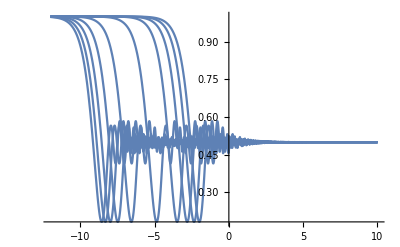

```mathematica
Plot[Rexp1/.{m2->Exp[x]},{x,-12,10}]
```

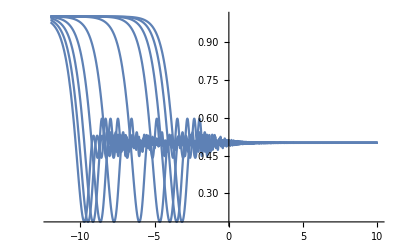

```mathematica
Plot[Rexp2/.{m2->Exp[x]},{x,-12,10}]
```

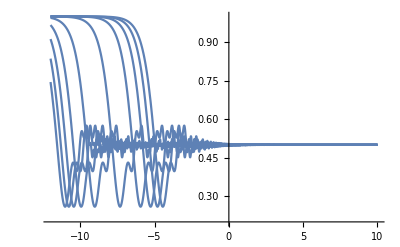

```mathematica
Plot[Rexp3/.{m2->Exp[x]},{x,-12,10},PlotRange->{0.2,1}]
```

```mathematica
expsubGeVulikeratioless=Table[{expsubGeVulikeless[[i]]/expmcsubGeVulikeless[[i]],((expsubGeVulikelesserror[[i]]/expmcsubGeVulikeless[[i]])^2+ (expsubGeVulikeless[[i]]expmcsubGeVulikelesserror/expmcsubGeVulikeless[[i]]^2)^2)^0.5},{i,1,10}]

expsubGeVμlikeratio=Table[{expsubGeVμlike[[i]]/expmcsubGeVμlike[[i]],((expsubGeVμlikeError[[i]]/expmcsubGeVμlike[[i]])^2+ (expsubGeVμlike[[i]]expmcsubGeVμlikeerror[[i]]/expmcsubGeVμlike[[i]]^2)^2)^0.5},{i,1,10}]

expMCMultiGeVμlikeratio=Table[{expMultiGeVμlike[[i]]/expMCMultiGeVμlike[[i]],((expMultiGeVμlikeerror[[i]]/expMCMultiGeVμlike[[i]])^2+ (expMultiGeVμlike[[i]]expMCMultiGeVμlikeerror/expMCMultiGeVμlike[[i]]^2)^2)^0.5},{i,1,10}]
```

{{0.602757,0.0636489},{0.566191,0.0620998},{0.710638,0.071154},{0.61975,0.0646099},{0.625896,0.0671133},{0.598252,0.0657877},{0.641945,0.0680005},{0.596796,0.0638425},{0.679054,0.0694728},{0.663514,0.0718532}}

{{0.680614,0.058198},{0.428916,0.0454773},{0.526138,0.0508559},{0.64618,0.0569249},{0.706619,0.0610315},{0.719163,0.0602328},{0.934888,0.070923},{0.89141,0.0636017},{0.934888,0.070923},{1.03272,0.0748474}}

{{0.466809,0.0577535},{0.505085,0.0599473},{0.439275,0.0530312},{0.523476,0.0537951},{0.605362,0.054875},{0.865359,0.0701558},{0.860007,0.0721004},{0.947897,0.0799583},{0.971234,0.0886141},{0.963192,0.0846847}}

```mathematica
Rexp=Join[Rexp1,Rexp2,Rexp3]
```

{(2.66657 (1.26222×10^-7 FresnelS[60.8723 √m2]-1.26222×10^-7 FresnelS[118.026 √m2]+√m2 (0.187507 m2-7.68343×10^-6 Sin[5820.5 m2]+0.0000148975 Sin[21881.6 m2])))/m2^(3/2),(2.66657 (1.83692×10^-7 FresnelS[53.7157 √m2]-1.83692×10^-7 FresnelS[104.15 √m2]+√m2 (0.187507 m2-9.86716×10^-6 Sin[4532.34 m2]+0.0000191316 Sin[17038.9 m2])))/m2^(3/2),(2.66657 (3.02861×10^-7 FresnelS[45.4692 √m2]-3.02861×10^-7 FresnelS[88.161 √m2]+√m2 (0.187507 m2-0.0000137709 Sin[3247.54 m2]+0.0000267005 Sin[12208.8 m2])))/m2^(3/2),(2.66657 (6.39215×10^-7 FresnelS[35.4473 √m2]-6.39215×10^-7 FresnelS[68.7293 √m2]+√m2 (0.187507 m2-0.0000226584 Sin[1973.72 m2]+0.0000439328 Sin[7420. m2])))/m2^(3/2),(2.66657 (2.52309×10^-6 FresnelS[22.4296 √m2]-2.52309×10^-6 FresnelS[43.4891 √m2]+√m2 (0.187507 m2-0.0000565917 Sin[790.245 m2]+0.000109727 Sin[2970.85 m2])))/m2^(3/2),(2.66657 (0.0000322926 FresnelS[9.58879 √m2]-0.0000322926 FresnelS[18.5919 √m2]+√m2 (0.187507 m2-0.000309647 Sin[144.427 m2]+0.00060038 Sin[542.958 m2])))/m2^(3/2),(2.66657 (0.000256669 FresnelS[4.80479 √m2]-0.000256669 FresnelS[9.31608 √m2]+√m2 (0.187507 m2-0.00123324 Sin[36.2634 m2]+0.00239115 Sin[136.328 m2])))/m2^(3/2),(2.66657 (0.000707607 FresnelS[3.42663 √m2]-0.000707607 FresnelS[6.64396 √m2]+√m2 (0.187507 m2-0.00242471 Sin[18.444 m2]+0.00470131 Sin[69.3383 m2])))/m2^(3/2),(2.66657 (0.00141593 FresnelS[2.71926 √m2]-0.00141593 FresnelS[5.27242 √m2]+√m2 (0.187507 m2-0.00385029 Sin[11.6151 m2]+0.00746538 Sin[43.6657 m2])))/m2^(3/2),(2.66657 (0.00241873 FresnelS[2.27476 √m2]-0.00241873 FresnelS[4.41058 √m2]+√m2 (0.187507 m2-0.00550203 Sin[8.12816 m2]+0.010668 Sin[30.557 m2])))/m2^(3/2),(0.572043 (0.87406 m2-0.0000171807 Sin[21881.6 m2]+0.0000171807 Sin[72756.2 m2]))/m2,(0.572043 (0.87406 m2-0.0000220636 Sin[17038.9 m2]+0.0000220636 Sin[56654.3 m2]))/m2,(0.572043 (0.87406 m2-0.0000307926 Sin[12208.8 m2]+0.0000307926 Sin[40594.2 m2]))/m2,(0.572043 (0.87406 m2-0.0000506658 Sin[7420. m2]+0.0000506658 Sin[24671.5 m2]))/m2,(0.572043 (0.87406 m2-0.000126543 Sin[2970.85 m2]+0.000126543 Sin[9878.07 m2]))/m2,(0.572043 (0.87406 m2-0.000692392 Sin[542.958 m2]+0.000692392 Sin[1805.33 m2]))/m2,(0.572043 (0.87406 m2-0.0027576 Sin[136.328 m2]+0.0027576 Sin[453.292 m2]))/m2,(0.572043 (0.87406 m2-0.00542182 Sin[69.3383 m2]+0.00542182 Sin[230.55 m2]))/m2,(0.572043 (0.87406 m2-0.0086095 Sin[43.6657 m2]+0.0086095 Sin[145.188 m2]))/m2,(0.572043 (0.87406 m2-0.0123029 Sin[30.557 m2]+0.0123029 Sin[101.602 m2]))/m2,1/m2 0.418117 (1.19584 m2+(0.+7.40293×10^-6 ⅈ) ((0.-36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-72756.2 ⅈ) m2]-(0.+7.40293×10^-6 ⅈ) ((0.+36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+72756.2 ⅈ) m2]-(0.+2.93785×10^-6 ⅈ) ((0.-145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-291025. ⅈ) m2]+(0.+2.93785×10^-6 ⅈ) ((0.+145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+291025. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+9.50693×10^-6 ⅈ) ((0.-28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-56654.3 ⅈ) m2]-(0.+9.50693×10^-6 ⅈ) ((0.+28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+56654.3 ⅈ) m2]-(0.+3.77283×10^-6 ⅈ) ((0.-113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-226617. ⅈ) m2]+(0.+3.77283×10^-6 ⅈ) ((0.+113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+226617. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.0000132681 ⅈ) ((0.-20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-40594.2 ⅈ) m2]-(0.+0.0000132681 ⅈ) ((0.+20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+40594.2 ⅈ) m2]-(0.+5.26546×10^-6 ⅈ) ((0.-81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-162377. ⅈ) m2]+(0.+5.26546×10^-6 ⅈ) ((0.+81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+162377. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.0000218312 ⅈ) ((0.-12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-24671.5 ⅈ) m2]-(0.+0.0000218312 ⅈ) ((0.+12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+24671.5 ⅈ) m2]-(0.+8.66373×10^-6 ⅈ) ((0.-49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-98686. ⅈ) m2]+(0.+8.66373×10^-6 ⅈ) ((0.+49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+98686. ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.0000545257 ⅈ) ((0.-4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-9878.07 ⅈ) m2]-(0.+0.0000545257 ⅈ) ((0.+4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+9878.07 ⅈ) m2]-(0.+0.0000216385 ⅈ) ((0.-19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-39512.3 ⅈ) m2]+(0.+0.0000216385 ⅈ) ((0.+19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+39512.3 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.000298343 ⅈ) ((0.-902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1805.33 ⅈ) m2]-(0.+0.000298343 ⅈ) ((0.+902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1805.33 ⅈ) m2]-(0.+0.000118397 ⅈ) ((0.-3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-7221.34 ⅈ) m2]+(0.+0.000118397 ⅈ) ((0.+3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+7221.34 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00118822 ⅈ) ((0.-226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-453.292 ⅈ) m2]-(0.+0.00118822 ⅈ) ((0.+226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+453.292 ⅈ) m2]-(0.+0.000471544 ⅈ) ((0.-906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1813.17 ⅈ) m2]+(0.+0.000471544 ⅈ) ((0.+906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1813.17 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00233619 ⅈ) ((0.-115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-230.55 ⅈ) m2]-(0.+0.00233619 ⅈ) ((0.+115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+230.55 ⅈ) m2]-(0.+0.000927118 ⅈ) ((0.-461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-922.2 ⅈ) m2]+(0.+0.000927118 ⅈ) ((0.+461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+922.2 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00370972 ⅈ) ((0.-72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-145.188 ⅈ) m2]-(0.+0.00370972 ⅈ) ((0.+72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+145.188 ⅈ) m2]-(0.+0.0014722 ⅈ) ((0.-290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-580.754 ⅈ) m2]+(0.+0.0014722 ⅈ) ((0.+290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+580.754 ⅈ) m2]),1/m2 0.418117 (1.19584 m2+(0.+0.00530116 ⅈ) ((0.-50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-101.602 ⅈ) m2]-(0.+0.00530116 ⅈ) ((0.+50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+101.602 ⅈ) m2]-(0.+0.00210377 ⅈ) ((0.-203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-406.408 ⅈ) m2]+(0.+0.00210377 ⅈ) ((0.+203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+406.408 ⅈ) m2])}

```mathematica
X2less=Sum[(Rexp[[i+20]]-expsubGeVulikeratioless[[i,1]])^2/expsubGeVulikeratioless[[i,2]]^2,{i,1,10}]
```

193.69 (-0.663514+1/m2 0.418117 (1.19584 m2+(0.+0.00530116 ⅈ) ((0.-50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-101.602 ⅈ) m2]-(0.+0.00530116 ⅈ) ((0.+50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+101.602 ⅈ) m2]-(0.+0.00210377 ⅈ) ((0.-203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-406.408 ⅈ) m2]+(0.+0.00210377 ⅈ) ((0.+203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+406.408 ⅈ) m2]))^2+207.191 (-0.679054+1/m2 0.418117 (1.19584 m2+(0.+0.00370972 ⅈ) ((0.-72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-145.188 ⅈ) m2]-(0.+0.00370972 ⅈ) ((0.+72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+145.188 ⅈ) m2]-(0.+0.0014722 ⅈ) ((0.-290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-580.754 ⅈ) m2]+(0.+0.0014722 ⅈ) ((0.+290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+580.754 ⅈ) m2]))^2+245.347 (-0.596796+1/m2 0.418117 (1.19584 m2+(0.+0.00233619 ⅈ) ((0.-115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-230.55 ⅈ) m2]-(0.+0.00233619 ⅈ) ((0.+115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+230.55 ⅈ) m2]-(0.+0.000927118 ⅈ) ((0.-461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-922.2 ⅈ) m2]+(0.+0.000927118 ⅈ) ((0.+461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+922.2 ⅈ) m2]))^2+216.26 (-0.641945+1/m2 0.418117 (1.19584 m2+(0.+0.00118822 ⅈ) ((0.-226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-453.292 ⅈ) m2]-(0.+0.00118822 ⅈ) ((0.+226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+453.292 ⅈ) m2]-(0.+0.000471544 ⅈ) ((0.-906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1813.17 ⅈ) m2]+(0.+0.000471544 ⅈ) ((0.+906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1813.17 ⅈ) m2]))^2+231.053 (-0.598252+1/m2 0.418117 (1.19584 m2+(0.+0.000298343 ⅈ) ((0.-902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1805.33 ⅈ) m2]-(0.+0.000298343 ⅈ) ((0.+902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1805.33 ⅈ) m2]-(0.+0.000118397 ⅈ) ((0.-3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-7221.34 ⅈ) m2]+(0.+0.000118397 ⅈ) ((0.+3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+7221.34 ⅈ) m2]))^2+222.016 (-0.625896+1/m2 0.418117 (1.19584 m2+(0.+0.0000545257 ⅈ) ((0.-4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-9878.07 ⅈ) m2]-(0.+0.0000545257 ⅈ) ((0.+4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+9878.07 ⅈ) m2]-(0.+0.0000216385 ⅈ) ((0.-19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-39512.3 ⅈ) m2]+(0.+0.0000216385 ⅈ) ((0.+19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+39512.3 ⅈ) m2]))^2+239.553 (-0.61975+1/m2 0.418117 (1.19584 m2+(0.+0.0000218312 ⅈ) ((0.-12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-24671.5 ⅈ) m2]-(0.+0.0000218312 ⅈ) ((0.+12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+24671.5 ⅈ) m2]-(0.+8.66373×10^-6 ⅈ) ((0.-49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-98686. ⅈ) m2]+(0.+8.66373×10^-6 ⅈ) ((0.+49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+98686. ⅈ) m2]))^2+197.516 (-0.710638+1/m2 0.418117 (1.19584 m2+(0.+0.0000132681 ⅈ) ((0.-20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-40594.2 ⅈ) m2]-(0.+0.0000132681 ⅈ) ((0.+20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+40594.2 ⅈ) m2]-(0.+5.26546×10^-6 ⅈ) ((0.-81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-162377. ⅈ) m2]+(0.+5.26546×10^-6 ⅈ) ((0.+81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+162377. ⅈ) m2]))^2+259.31 (-0.566191+1/m2 0.418117 (1.19584 m2+(0.+9.50693×10^-6 ⅈ) ((0.-28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-56654.3 ⅈ) m2]-(0.+9.50693×10^-6 ⅈ) ((0.+28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+56654.3 ⅈ) m2]-(0.+3.77283×10^-6 ⅈ) ((0.-113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-226617. ⅈ) m2]+(0.+3.77283×10^-6 ⅈ) ((0.+113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+226617. ⅈ) m2]))^2+246.841 (-0.602757+1/m2 0.418117 (1.19584 m2+(0.+7.40293×10^-6 ⅈ) ((0.-36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-72756.2 ⅈ) m2]-(0.+7.40293×10^-6 ⅈ) ((0.+36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+72756.2 ⅈ) m2]-(0.+2.93785×10^-6 ⅈ) ((0.-145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-291025. ⅈ) m2]+(0.+2.93785×10^-6 ⅈ) ((0.+145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+291025. ⅈ) m2]))^2

```mathematica
X2more=Sum[(Rexp[[i+10]]-expsubGeVμlikeratio[[i,1]])^2/expsubGeVμlikeratio[[i,2]]^2,{i,1,10}]
X2multi=Sum[(Rexp[[i]]-expMCMultiGeVμlikeratio[[i,1]])^2/expMCMultiGeVμlikeratio[[i,2]]^2,{i,1,10}]
```

178.503 (-1.03272+(0.572043 (0.87406 m2-0.0123029 Sin[30.557 m2]+0.0123029 Sin[101.602 m2]))/m2)^2+198.804 (-0.934888+(0.572043 (0.87406 m2-0.0086095 Sin[43.6657 m2]+0.0086095 Sin[145.188 m2]))/m2)^2+247.208 (-0.89141+(0.572043 (0.87406 m2-0.00542182 Sin[69.3383 m2]+0.00542182 Sin[230.55 m2]))/m2)^2+198.804 (-0.934888+(0.572043 (0.87406 m2-0.0027576 Sin[136.328 m2]+0.0027576 Sin[453.292 m2]))/m2)^2+275.635 (-0.719163+(0.572043 (0.87406 m2-0.000692392 Sin[542.958 m2]+0.000692392 Sin[1805.33 m2]))/m2)^2+268.467 (-0.706619+(0.572043 (0.87406 m2-0.000126543 Sin[2970.85 m2]+0.000126543 Sin[9878.07 m2]))/m2)^2+308.6 (-0.64618+(0.572043 (0.87406 m2-0.0000506658 Sin[7420. m2]+0.0000506658 Sin[24671.5 m2]))/m2)^2+386.649 (-0.526138+(0.572043 (0.87406 m2-0.0000307926 Sin[12208.8 m2]+0.0000307926 Sin[40594.2 m2]))/m2)^2+483.516 (-0.428916+(0.572043 (0.87406 m2-0.0000220636 Sin[17038.9 m2]+0.0000220636 Sin[56654.3 m2]))/m2)^2+295.246 (-0.680614+(0.572043 (0.87406 m2-0.0000171807 Sin[21881.6 m2]+0.0000171807 Sin[72756.2 m2]))/m2)^2

139.441 (-0.963192+(2.66657 (0.00241873 FresnelS[2.27476 √m2]-0.00241873 FresnelS[4.41058 √m2]+√m2 (0.187507 m2-0.00550203 Sin[8.12816 m2]+0.010668 Sin[30.557 m2])))/m2^(3/2))^2+127.349 (-0.971234+(2.66657 (0.00141593 FresnelS[2.71926 √m2]-0.00141593 FresnelS[5.27242 √m2]+√m2 (0.187507 m2-0.00385029 Sin[11.6151 m2]+0.00746538 Sin[43.6657 m2])))/m2^(3/2))^2+156.413 (-0.947897+(2.66657 (0.000707607 FresnelS[3.42663 √m2]-0.000707607 FresnelS[6.64396 √m2]+√m2 (0.187507 m2-0.00242471 Sin[18.444 m2]+0.00470131 Sin[69.3383 m2])))/m2^(3/2))^2+192.364 (-0.860007+(2.66657 (0.000256669 FresnelS[4.80479 √m2]-0.000256669 FresnelS[9.31608 √m2]+√m2 (0.187507 m2-0.00123324 Sin[36.2634 m2]+0.00239115 Sin[136.328 m2])))/m2^(3/2))^2+203.176 (-0.865359+(2.66657 (0.0000322926 FresnelS[9.58879 √m2]-0.0000322926 FresnelS[18.5919 √m2]+√m2 (0.187507 m2-0.000309647 Sin[144.427 m2]+0.00060038 Sin[542.958 m2])))/m2^(3/2))^2+332.086 (-0.605362+(2.66657 (2.52309×10^-6 FresnelS[22.4296 √m2]-2.52309×10^-6 FresnelS[43.4891 √m2]+√m2 (0.187507 m2-0.0000565917 Sin[790.245 m2]+0.000109727 Sin[2970.85 m2])))/m2^(3/2))^2+345.553 (-0.523476+(2.66657 (6.39215×10^-7 FresnelS[35.4473 √m2]-6.39215×10^-7 FresnelS[68.7293 √m2]+√m2 (0.187507 m2-0.0000226584 Sin[1973.72 m2]+0.0000439328 Sin[7420. m2])))/m2^(3/2))^2+355.58 (-0.439275+(2.66657 (3.02861×10^-7 FresnelS[45.4692 √m2]-3.02861×10^-7 FresnelS[88.161 √m2]+√m2 (0.187507 m2-0.0000137709 Sin[3247.54 m2]+0.0000267005 Sin[12208.8 m2])))/m2^(3/2))^2+278.267 (-0.505085+(2.66657 (1.83692×10^-7 FresnelS[53.7157 √m2]-1.83692×10^-7 FresnelS[104.15 √m2]+√m2 (0.187507 m2-9.86716×10^-6 Sin[4532.34 m2]+0.0000191316 Sin[17038.9 m2])))/m2^(3/2))^2+299.808 (-0.466809+(2.66657 (1.26222×10^-7 FresnelS[60.8723 √m2]-1.26222×10^-7 FresnelS[118.026 √m2]+√m2 (0.187507 m2-7.68343×10^-6 Sin[5820.5 m2]+0.0000148975 Sin[21881.6 m2])))/m2^(3/2))^2

```mathematica
X2tot=X2less+X2more+X2multi
```

193.69 (-0.663514+1/m2 0.418117 (1.19584 m2+(0.+0.00530116 ⅈ) ((0.-50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-101.602 ⅈ) m2]-(0.+0.00530116 ⅈ) ((0.+50.801 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+101.602 ⅈ) m2]-(0.+0.00210377 ⅈ) ((0.-203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-406.408 ⅈ) m2]+(0.+0.00210377 ⅈ) ((0.+203.204 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+406.408 ⅈ) m2]))^2+207.191 (-0.679054+1/m2 0.418117 (1.19584 m2+(0.+0.00370972 ⅈ) ((0.-72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-145.188 ⅈ) m2]-(0.+0.00370972 ⅈ) ((0.+72.5942 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+145.188 ⅈ) m2]-(0.+0.0014722 ⅈ) ((0.-290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-580.754 ⅈ) m2]+(0.+0.0014722 ⅈ) ((0.+290.377 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+580.754 ⅈ) m2]))^2+245.347 (-0.596796+1/m2 0.418117 (1.19584 m2+(0.+0.00233619 ⅈ) ((0.-115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-230.55 ⅈ) m2]-(0.+0.00233619 ⅈ) ((0.+115.275 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+230.55 ⅈ) m2]-(0.+0.000927118 ⅈ) ((0.-461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-922.2 ⅈ) m2]+(0.+0.000927118 ⅈ) ((0.+461.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+922.2 ⅈ) m2]))^2+216.26 (-0.641945+1/m2 0.418117 (1.19584 m2+(0.+0.00118822 ⅈ) ((0.-226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-453.292 ⅈ) m2]-(0.+0.00118822 ⅈ) ((0.+226.646 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+453.292 ⅈ) m2]-(0.+0.000471544 ⅈ) ((0.-906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1813.17 ⅈ) m2]+(0.+0.000471544 ⅈ) ((0.+906.584 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1813.17 ⅈ) m2]))^2+231.053 (-0.598252+1/m2 0.418117 (1.19584 m2+(0.+0.000298343 ⅈ) ((0.-902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-1805.33 ⅈ) m2]-(0.+0.000298343 ⅈ) ((0.+902.667 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+1805.33 ⅈ) m2]-(0.+0.000118397 ⅈ) ((0.-3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-7221.34 ⅈ) m2]+(0.+0.000118397 ⅈ) ((0.+3610.67 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+7221.34 ⅈ) m2]))^2+222.016 (-0.625896+1/m2 0.418117 (1.19584 m2+(0.+0.0000545257 ⅈ) ((0.-4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-9878.07 ⅈ) m2]-(0.+0.0000545257 ⅈ) ((0.+4939.03 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+9878.07 ⅈ) m2]-(0.+0.0000216385 ⅈ) ((0.-19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-39512.3 ⅈ) m2]+(0.+0.0000216385 ⅈ) ((0.+19756.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+39512.3 ⅈ) m2]))^2+239.553 (-0.61975+1/m2 0.418117 (1.19584 m2+(0.+0.0000218312 ⅈ) ((0.-12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-24671.5 ⅈ) m2]-(0.+0.0000218312 ⅈ) ((0.+12335.7 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+24671.5 ⅈ) m2]-(0.+8.66373×10^-6 ⅈ) ((0.-49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-98686. ⅈ) m2]+(0.+8.66373×10^-6 ⅈ) ((0.+49343. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+98686. ⅈ) m2]))^2+197.516 (-0.710638+1/m2 0.418117 (1.19584 m2+(0.+0.0000132681 ⅈ) ((0.-20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-40594.2 ⅈ) m2]-(0.+0.0000132681 ⅈ) ((0.+20297.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+40594.2 ⅈ) m2]-(0.+5.26546×10^-6 ⅈ) ((0.-81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-162377. ⅈ) m2]+(0.+5.26546×10^-6 ⅈ) ((0.+81188.4 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+162377. ⅈ) m2]))^2+259.31 (-0.566191+1/m2 0.418117 (1.19584 m2+(0.+9.50693×10^-6 ⅈ) ((0.-28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-56654.3 ⅈ) m2]-(0.+9.50693×10^-6 ⅈ) ((0.+28327.2 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+56654.3 ⅈ) m2]-(0.+3.77283×10^-6 ⅈ) ((0.-113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-226617. ⅈ) m2]+(0.+3.77283×10^-6 ⅈ) ((0.+113309. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+226617. ⅈ) m2]))^2+246.841 (-0.602757+1/m2 0.418117 (1.19584 m2+(0.+7.40293×10^-6 ⅈ) ((0.-36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.-72756.2 ⅈ) m2]-(0.+7.40293×10^-6 ⅈ) ((0.+36378.1 ⅈ) m2)^(2/3) Gamma[0.333333,(0.+72756.2 ⅈ) m2]-(0.+2.93785×10^-6 ⅈ) ((0.-145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.-291025. ⅈ) m2]+(0.+2.93785×10^-6 ⅈ) ((0.+145512. ⅈ) m2)^(2/3) Gamma[0.333333,(0.+291025. ⅈ) m2]))^2+139.441 (-0.963192+(2.66657 (0.00241873 FresnelS[2.27476 √m2]-0.00241873 FresnelS[4.41058 √m2]+√m2 (0.187507 m2-0.00550203 Sin[8.12816 m2]+0.010668 Sin[30.557 m2])))/m2^(3/2))^2+127.349 (-0.971234+(2.66657 (0.00141593 FresnelS[2.71926 √m2]-0.00141593 FresnelS[5.27242 √m2]+√m2 (0.187507 m2-0.00385029 Sin[11.6151 m2]+0.00746538 Sin[43.6657 m2])))/m2^(3/2))^2+156.413 (-0.947897+(2.66657 (0.000707607 FresnelS[3.42663 √m2]-0.000707607 FresnelS[6.64396 √m2]+√m2 (0.187507 m2-0.00242471 Sin[18.444 m2]+0.00470131 Sin[69.3383 m2])))/m2^(3/2))^2+178.503 (-1.03272+(0.572043 (0.87406 m2-0.0123029 Sin[30.557 m2]+0.0123029 Sin[101.602 m2]))/m2)^2+192.364 (-0.860007+(2.66657 (0.000256669 FresnelS[4.80479 √m2]-0.000256669 FresnelS[9.31608 √m2]+√m2 (0.187507 m2-0.00123324 Sin[36.2634 m2]+0.00239115 Sin[136.328 m2])))/m2^(3/2))^2+198.804 (-0.934888+(0.572043 (0.87406 m2-0.0086095 Sin[43.6657 m2]+0.0086095 Sin[145.188 m2]))/m2)^2+247.208 (-0.89141+(0.572043 (0.87406 m2-0.00542182 Sin[69.3383 m2]+0.00542182 Sin[230.55 m2]))/m2)^2+198.804 (-0.934888+(0.572043 (0.87406 m2-0.0027576 Sin[136.328 m2]+0.0027576 Sin[453.292 m2]))/m2)^2+203.176 (-0.865359+(2.66657 (0.0000322926 FresnelS[9.58879 √m2]-0.0000322926 FresnelS[18.5919 √m2]+√m2 (0.187507 m2-0.000309647 Sin[144.427 m2]+0.00060038 Sin[542.958 m2])))/m2^(3/2))^2+275.635 (-0.719163+(0.572043 (0.87406 m2-0.000692392 Sin[542.958 m2]+0.000692392 Sin[1805.33 m2]))/m2)^2+332.086 (-0.605362+(2.66657 (2.52309×10^-6 FresnelS[22.4296 √m2]-2.52309×10^-6 FresnelS[43.4891 √m2]+√m2 (0.187507 m2-0.0000565917 Sin[790.245 m2]+0.000109727 Sin[2970.85 m2])))/m2^(3/2))^2+345.553 (-0.523476+(2.66657 (6.39215×10^-7 FresnelS[35.4473 √m2]-6.39215×10^-7 FresnelS[68.7293 √m2]+√m2 (0.187507 m2-0.0000226584 Sin[1973.72 m2]+0.0000439328 Sin[7420. m2])))/m2^(3/2))^2+268.467 (-0.706619+(0.572043 (0.87406 m2-0.000126543 Sin[2970.85 m2]+0.000126543 Sin[9878.07 m2]))/m2)^2+355.58 (-0.439275+(2.66657 (3.02861×10^-7 FresnelS[45.4692 √m2]-3.02861×10^-7 FresnelS[88.161 √m2]+√m2 (0.187507 m2-0.0000137709 Sin[3247.54 m2]+0.0000267005 Sin[12208.8 m2])))/m2^(3/2))^2+278.267 (-0.505085+(2.66657 (1.83692×10^-7 FresnelS[53.7157 √m2]-1.83692×10^-7 FresnelS[104.15 √m2]+√m2 (0.187507 m2-9.86716×10^-6 Sin[4532.34 m2]+0.0000191316 Sin[17038.9 m2])))/m2^(3/2))^2+299.808 (-0.466809+(2.66657 (1.26222×10^-7 FresnelS[60.8723 √m2]-1.26222×10^-7 FresnelS[118.026 √m2]+√m2 (0.187507 m2-7.68343×10^-6 Sin[5820.5 m2]+0.0000148975 Sin[21881.6 m2])))/m2^(3/2))^2+308.6 (-0.64618+(0.572043 (0.87406 m2-0.0000506658 Sin[7420. m2]+0.0000506658 Sin[24671.5 m2]))/m2)^2+386.649 (-0.526138+(0.572043 (0.87406 m2-0.0000307926 Sin[12208.8 m2]+0.0000307926 Sin[40594.2 m2]))/m2)^2+483.516 (-0.428916+(0.572043 (0.87406 m2-0.0000220636 Sin[17038.9 m2]+0.0000220636 Sin[56654.3 m2]))/m2)^2+295.246 (-0.680614+(0.572043 (0.87406 m2-0.0000171807 Sin[21881.6 m2]+0.0000171807 Sin[72756.2 m2]))/m2)^2

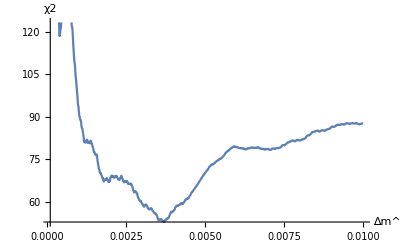

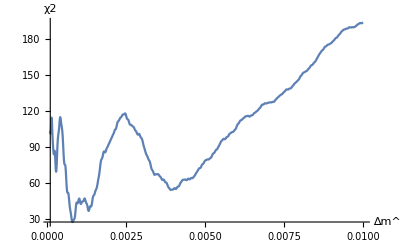

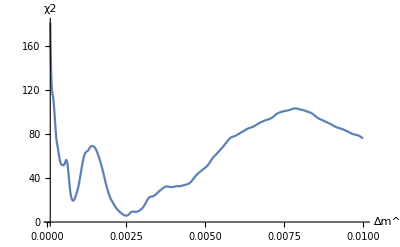

```mathematica
lessplot=Plot[X2less/. {m2-> x},{x,10^-4,10^-2}, AxesLabel->{"∆m^2","χ2"}]
moreplot=Plot[X2more/. {m2-> x},{x,10^-4,10^-2},AxesLabel->{"∆m^2","χ2"}]
multiplot=Plot[X2multi/. {m2-> x},{x,10^-4,10^-2},AxesLabel->{"∆m^2","χ2"}]
```

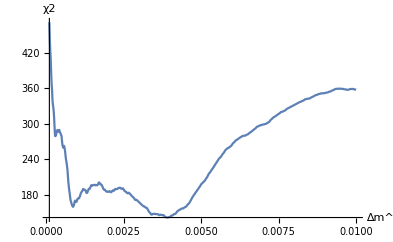

```mathematica
totplot=Plot[X2tot /. {m2 -> x}, {x, 10^-4, 10^-2},AxesLabel->{"∆m^2","χ2"}]
```

```mathematica
minless=FindMinimum[X2less/. {m2-> x},{x,0.0037,0.004}]
```

{52.8358,{x→0.00369439}}

```mathematica
minmore=FindMinimum[X2more/. {m2-> x},{x,0.0005,0.002}]
```

{27.0807,{x→0.000804713}}

```mathematica
minmulti=FindMinimum[X2multi/. {m2-> x},{x,0.0025,0.002}]
```

{5.825,{x→0.00249829}}

```mathematica
mintot=FindMinimum[X2tot/. {m2-> x},{x,0.0035,0.004}]
```

{147.92,{x→0.00350098}}

```mathematica
mless=minless[[1]]+9
mmore=minmore[[1]]+9
mmulti=minmulti[[1]]+9
mtot=mintot[[1]]+9
```

61.8358

36.0807

14.825

156.92

```mathematica
threesigmaplotless=Plot[mless,{x,10^-4,10^-2},PlotStyle->Orange];
threesigmaplotmore=Plot[mmore,{x,10^-4,10^-2},PlotStyle->Orange];
threesigmaplotmutli=Plot[mmulti,{x,10^-4,10^-2},PlotStyle->Orange];
threesigmaplotmtot=Plot[mtot,{x,10^-4,10^-2},PlotStyle->Orange];
```

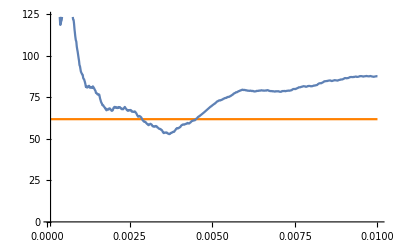

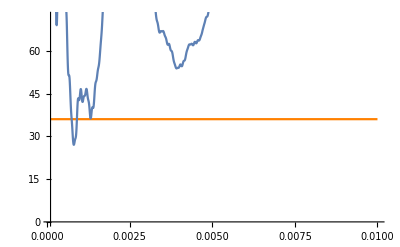

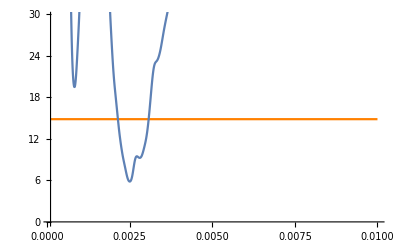

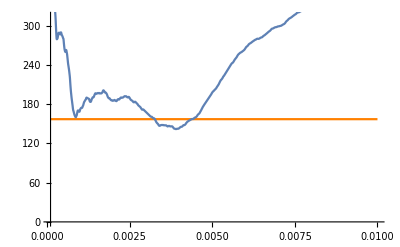

```mathematica
Show[{threesigmaplotless,lessplot}]
Show[{threesigmaplotmore,moreplot}]
Show[{threesigmaplotmutli,multiplot}]
Show[{threesigmaplotmtot,totplot}]
```

```mathematica
Chop[FindRoot[X2less==mless,{m2,0.002}]]
Chop[FindRoot[X2less==mless,{m2,0.003}]]

FindRoot[X2more==mmore,{m2,0.0002,0.0008}]
FindRoot[X2more==mmore,{m2,0.0015,0.0008}]

FindRoot[X2multi==mmulti,{m2,0.002}]
FindRoot[X2multi==mmulti,{m2,0.003}]

Chop[FindRoot[X2tot==mtot,{m2,0.003}]]
Chop[FindRoot[X2tot==mtot,{m2,0.004}]]
```

{m2→0.00450326}

{m2→0.00287103}

{m2→0.000739575}

{m2→0.000898796}

{m2→0.00214031}

{m2→0.00307129}

{m2→0.00325814}

{m2→0.00436749}

```mathematica
Table[{{costheta[[i]],expsubGeVulikeratioless[[i,1]]},ErrorBar[0.1,expsubGeVulikeratioless[[i,2]]]},{i,1,10}]
```

{{{-0.9,0.602757},ErrorBar[0.1,0.0636489]},{{-0.7,0.566191},ErrorBar[0.1,0.0620998]},{{-0.5,0.710638},ErrorBar[0.1,0.071154]},{{-0.3,0.61975},ErrorBar[0.1,0.0646099]},{{-0.1,0.625896},ErrorBar[0.1,0.0671133]},{{0.1,0.598252},ErrorBar[0.1,0.0657877]},{{0.3,0.641945},ErrorBar[0.1,0.0680005]},{{0.5,0.596796},ErrorBar[0.1,0.0638425]},{{0.7,0.679054},ErrorBar[0.1,0.0694728]},{{0.9,0.663514},ErrorBar[0.1,0.0718532]}}

```mathematica
(*X2lessbestfit=ErrorListPlot[Table[{{costheta[[i]],expsubGeVulikeratioless[[i,1]]},ErrorBar[0.1,expsubGeVulikeratioless[[i,2]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotStyle->Red,PlotRange->{{-1,1},{0,1.1}}]*)
```

```mathematica
Rexp1bestfittot=ListPlot[Transpose[{costheta,Rexp3/.{m2->x}/.mintot[[2]]}]];
```

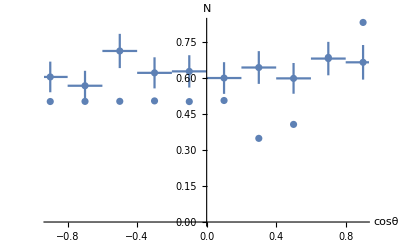

```mathematica
Show[{Rexp1bestfittot,plotexpsubGeVulikeratioless}, AxesLabel-> {"cosθ","N"}]
```

```mathematica
Rexp2bestfittot=ListPlot[Transpose[{costheta,Rexp2/.{m2->x}/.mintot[[2]]}]];
```

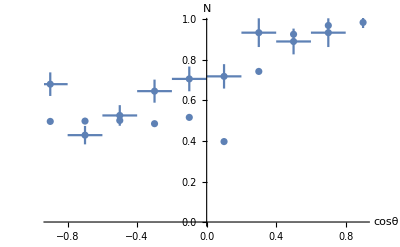

```mathematica
Show[{Rexp2bestfittot,plotexpsubGeVμlikeratio}, AxesLabel-> {"cosθ","N"}]
```

```mathematica
Rexp3bestfittot=ListPlot[Transpose[{costheta,Rexp1/.{m2->x}/.mintot[[2]]}]];
```

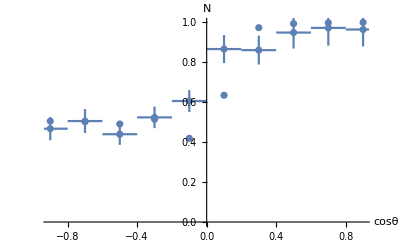

```mathematica
Show[{Rexp3bestfittot,plotexpMCMultiGeVμlikeratio}, AxesLabel-> {"cosθ","N"}]
```

```mathematica
Rexp1bestfitmulti=ListPlot[Transpose[{costheta,Rexp3/.{m2->x}/.minmulti[[2]]}]];
```

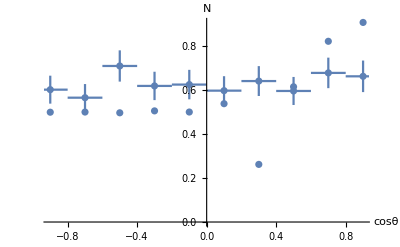

```mathematica
Show[{Rexp1bestfitmulti,plotexpsubGeVulikeratioless}, AxesLabel-> {"cosθ","N"}]
```

```mathematica
Rexp2bestfitmulti=ListPlot[Transpose[{costheta,Rexp2/.{m2->x}/.minmulti[[2]]}]];
```

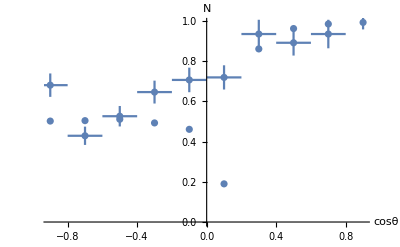

```mathematica
Show[{Rexp2bestfitmulti,plotexpsubGeVμlikeratio}, AxesLabel-> {"cosθ","N"}]
```

```mathematica
Rexp3bestfitmulti=ListPlot[Transpose[{costheta,Rexp1/.{m2->x}/.minmulti[[2]]}]];
```

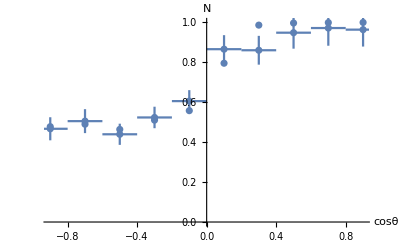

```mathematica
Show[{Rexp3bestfitmulti,plotexpMCMultiGeVμlikeratio}, AxesLabel-> {"cosθ","N"}]
```

```mathematica
(*X2morebestfit=ErrorListPlot[Table[{{costheta[[i]],expsubGeVulikeratioless[[i,1]]},ErrorBar[0.1,expsubGeVulikeratioless[[i,2]]]},{i,1,10}],
Axes->None,Frame->True,AspectRatio->1,PlotStyle->Red,PlotRange->{{-1,1},{0,1.1}}]*)
```